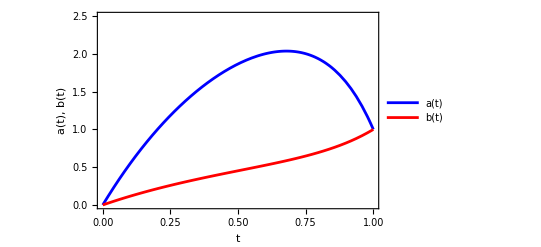
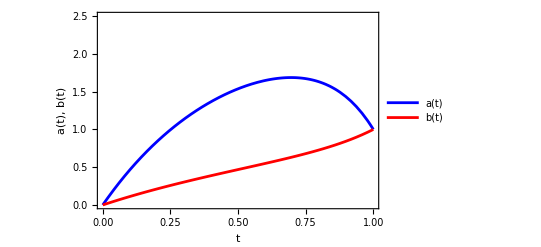
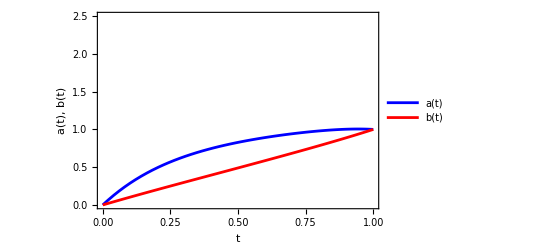
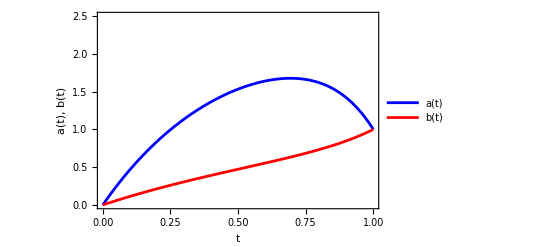
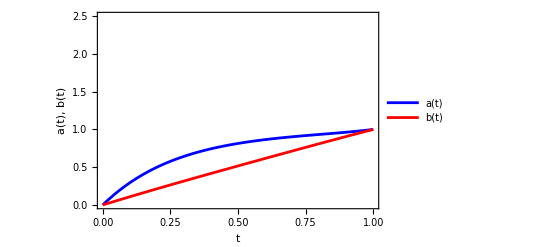
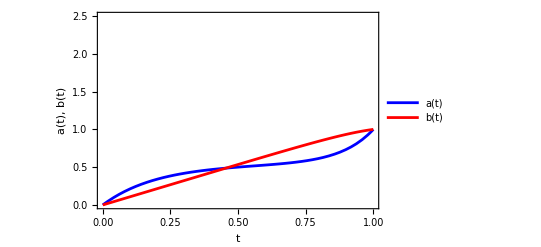
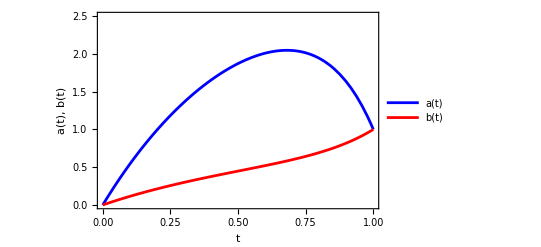
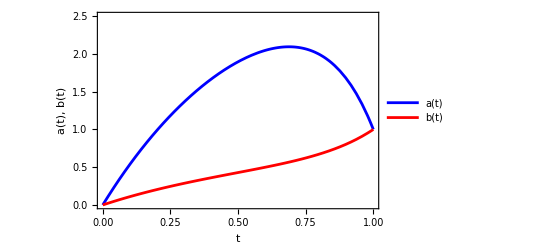
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Define constants*)
λ=5; κ=5; σ=0.5; (*Increased value for effect*)

(*Define the system of differential equations*)
solveSystem[ξa_,ξb_]:=Module[{eqns,bcs,sol,aSol,bSol},
eqns={
a''[t]==-(λ/2) (b''[t]+κ b'[t])+ξa σ^2 a[t],
b''[t]==-(1/(2 λ)) (a''[t]+κ a'[t])+(ξb/λ^2) σ^2 b[t]
};
bcs={a[0]==0,a[1]==1,b[0]==0,b[1]==1};
sol=DSolve[{eqns,bcs},{a[t],b[t]},t];
{a[t]/. sol[[1]],b[t]/. sol[[1]]}];

(*Define the grid of ξa and ξb values,multiplied by 3*)
xiValues={
{{1.5,1.5},{10,10},{50,50}},
{{10,1.5},{50,1.5},{100,1.5}},
{{1.5,10},{1.5,50},{1.5,100}}
};

(*Generate the 3x3 grid of plots*)
gridPlots=Grid[Table[
Module[{aSol,bSol,ξa=xiValues[[i,j,1]],ξb=xiValues[[i,j,2]]},
{aSol,bSol}=solveSystem[ξa,ξb];
Plot[{aSol,bSol},{t,0,1},
PlotLegends->{"a(t)","b(t)"},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{{"a(t), b(t)","κ="<>ToString[κ]<>", λ="<>ToString[λ]},{"t","ξ_a = "<>ToString[ξa]<>", ξ_b = "<>ToString[ξb]<>", σ="<>ToString[σ]}},PlotRange->{{0,1},{0,2.5}}]
],{i,1,3},{j,1,3}],Frame->All
];

(*Display the grid of plots*)
gridPlots
```

### Calculate Sine Coefficients

```mathematica
(*Define the function*)
f[x_]:=x^2-x

(*Calculate the sine coefficients manually*)
sinCoefficient[n_]:=2 Integrate[f[x] Sin[n π x],{x,0, 1}]

(*Calculate the first 10 sine coefficients*)
sinCoefficients=Table[sinCoefficient[n],{n,1,10}]

(*Convert coefficients to decimal numbers*)
decimalCoefficients=N[sinCoefficients]

(*Display the result*)
decimalCoefficients
```

{-8/π^3,0,-8/(27 π^3),0,-8/(125 π^3),0,-8/(343 π^3),0,-8/(729 π^3),0}

{-0.258012,0.,-0.00955601,0.,-0.0020641,0.,-0.000752222,0.,-0.000353926,0.}

{-0.258012,0.,-0.00955601,0.,-0.0020641,0.,-0.000752222,0.,-0.000353926,0.}

#### Check closed form vs. approximated Cost Function

```mathematica
(*Define the exogenous inputs as functions of t*)
a[t_]:=Sin[pi t] + 0.5 Sin[2 pi t]  (*Define a(t) here*)
(*b[t_]:=t^0.1 *)
b[t] := -Sin[pi t] -5 Sin[2 pi t] (*Define b(t) here*)

(*Define the derivatives of the exogenous inputs*)
aPrime[t_]:=D[a[t],t]
bPrime[t_]:=D[b[t],t]

(*Define the parameters*)
λ= 1(*Define λ here*);
k=1 (*Define k here*);

(*Define the functionals*)
functional1=(aPrime[t]+λ bPrime[t]) aPrime[t];
functional2=k (a[t]+λ b[t]) aPrime[t];

(*Calculate the integrals*)
integral1=Integrate[functional1,{t,0,1}]
integral2=Integrate[functional2,{t,0,1}]
total_cost = integral1 + integral2

(*Print the total cost*)Print["Total cost: ",N[total_cost]];
```

-1.5 pi (3 Sin[pi]+Sin[3 pi])-1.125 pi (4 pi+Sin[4 pi])

-3.+3. Cos[pi]^3-1.125 Sin[2 pi]^2

-3.+3. Cos[pi]^3-1.125 Sin[2 pi]^2-1.5 pi (3 Sin[pi]+Sin[3 pi])-1.125 pi (4 pi+Sin[4 pi])

Total cost: total_cost

```mathematica
total_cost
```

#### Another version that also prints the total cost

```mathematica
ClearAll;
(*Define the exogenous inputs as functions of t*)
a[t_]:=t (*Define a(t) here*)
b[t_]:=Sinh[6 * t] / Sinh[6] (*Define b(t) here*)

(*Define the derivatives of the exogenous inputs*)
aPrime[t_]:=D[a[t],t]
bPrime[t_]:=D[b[t],t]

(*Define the parameters*)
λ=6  (*Define λ here*)
k=1  (*Define k here*)

(*Define the functionals*)
functional1=(aPrime[t]+λ bPrime[t]) aPrime[t];
functional2=k (a[t]+λ b[t]) aPrime[t];

(*Calculate the integrals*)
integral1=Integrate[functional1,{t,0,1}]
integral2=Integrate[functional2,{t,0,1}]

(*Evaluate the integrals and total cost*)
{N[integral1],N[integral2],N[Evaluate[integral1+integral2]]}
```

6

1

7

1/2+Coth[6]-Csch[6]

{7.,1.49505,8.49505}

### Check Fourier Sine Transform

#### Evaluate Derivative

```mathematica
Module[{f,tPrime,tValue,tPrimeValue},
(*Define the function*)
f[t_]:=t^4-t;

(*Calculate the derivative symbolically*)
tPrime=D[f[t],t];

(*Define evaluation point*)
tValue=0.5;

(*Evaluate the derivative at the specific point*)
tPrimeValue=tPrime/. t->tValue;

(*Print the desired outputs*)
Print["Formula for tPrime: ",tPrime];
Print["Value of tPrime at t = ",tValue,": ",tPrimeValue];
]
```

Formula for tPrime: -1+4 t^3

Value of tPrime at t = 0.5: -0.5

#### Evaluate Second Derivative

```mathematica
Module[
{f,tPrime,tDoublePrime,tValue,tPrimeValue,tDoublePrimeValue},
(*Define the function*)
f[t_]:=t^3-t;

(*Calculate the first derivative symbolically*)
tPrime=D[f[t],t];

(*Calculate the second derivative symbolically*)
tDoublePrime=D[tPrime,t];

(*Define evaluation point*)
tValue=0.5;

(*Evaluate the first derivative at the specific point*)
tPrimeValue=tPrime/. t->tValue;

(*Evaluate the second derivative at the specific point*)tDoublePrimeValue=tDoublePrime/. t->tValue;

(*Print the desired outputs*)
Print["Formula for tPrime: ",tPrime];
Print["Value of tPrime at t = ",tValue,": ",tPrimeValue];
Print["Formula for tDoublePrime: ",tDoublePrime];
Print["Value of tDoublePrime at t = ",tValue,": ",tDoublePrimeValue];
]
```

Formula for tPrime: -1+3 t^2

Value of tPrime at t = 0.5: -0.25

Formula for tDoublePrime: 6 t

Value of tDoublePrime at t = 0.5: 3.

### Experiment with different b(t) specifications

```mathematica
Manipulate[
Plot[
x+c (0.25-(x-0.5)^2),
{x,0,1},
PlotRange->{{0,1}, All},
AxesLabel->{"x","f(x)"},
PlotLabel->"Plot of x + c * (0.25 - (x - 0.5)^2)"],
{{c,0}, -5,5}]
```

```mathematica
(*Define the function*)
f[x_,c_]:=x+c (0.25-(x-0.5)^2);

(*Calculate the first derivative*)
fPrime=D[f[x,c],x];

(*Calculate the second derivative*)
fDoublePrime=D[fPrime,x];

(*Display the results*)
fPrime
fDoublePrime
```

1-2 c (-0.5+x)

-2 c